```mathematica
mh=1.00794;
mc=12.011;
```

Inputs

```mathematica
r1FName="h.txt";
r2FName="ch4.txt";
```

Point groups

```mathematica
r1PG="";
r2PG="td";
tsPG="c3v";
```

Reactant 1 masses

```mathematica
r1mass={mh};
```

Reactant 1 electronic splitting, eV

```mathematica
r1Elec=Infinity;
```

Reactant 1 g.s. electronic degeneracy

```mathematica
r1g0=2;
```

Reactant 2 masses

```mathematica
r2mass={mc,mh,mh,mh,mh};
```

Reactant 2 electronic splitting, eV

```mathematica
r2Elec=Infinity;
```

Reactant 2 g.s. electronic degeneracy

```mathematica
r2g0=1;
```

TS masses

```mathematica
tsmass={mc,mh,mh,mh,mh,mh};
```

Temperatures (K) of interest

```mathematica
temps=Join[Table[1000/i,{i,1,4,0.1}],{200,250,300,350,400,450,500,600,700,800,1000}];
```

Load packages

```mathematica
Needs["readInTxt`"];
Needs["PartFunc`"];
Needs["RectilProj`"];
Needs["Anharmonicities`"];
Needs["SCTST2`"];
SetDirectory[NotebookDirectory[]];
```

Constant parameters

Speed of light, cm/s

```mathematica
ccm=2.997925*^10;
```

a_0 in meters

```mathematica
mpera0=5.29177249*^-11;
```

Planck constant, Js

```mathematica
h=6.6260755*^-34;
```

Hartree in J

```mathematica
Eh=4.359748*^-18;
```

Boltzmann constant, J/K

```mathematica
kb=1.380650*^-23;
```

Da in kg

```mathematica
kgperamu=1.660538922*^-27;
```

Reactant 1 partition functions

```mathematica
r1Data=readInTxtAtom[r1FName,2];
```

```mathematica
r1NonElecQ=nonElecPartAtom[Total[r1mass],temps];
r1ElecQ=r1g0+Exp[-r1Elec*1.602177*^-19/kb/temps];
```

Reactant 2 partition functions

```mathematica
r2Data=readInTxt[r2FName,Length[r2mass],3];
```

```mathematica
r2NonElecQ=nonElecPartMol[r2Data[[1]],r2Data[[2]],r2mass,r2PG,temps];
r2ElecQ=r2g0+Exp[-r2Elec*1.602177*^-19/kb/temps];
```

TS partition functions

```mathematica
tsData=readInTxt["ts.txt",Length[tsmass],3];
```

```mathematica
tsNonVibNonElecQ=nonElecnonVibPartTS[tsData[[1]],tsmass,tsPG,temps];
tsElecQ=2;
```

Vibrationally adiabatic TST barrier height, a.u.

```mathematica
r2Freq=Delete[RectilProj[r2Data[[1]],r2Data[[2]],r2mass,{{1,2},{2,3}},"pre"][[1]],{{-1},{-2},{-3},{-4},{-5},{-6}}];
```

```mathematica
tsFreq={1642.9418393127726 ⅈ,3291.5703900214467,3290.1142308340095,3133.4778870720193,1948.1442930927615,1473.161733292422,1469.6580201297982,1151.7576317758617,1148.0926865165359,1090.1392266961998,591.9685269335691,576.7369529481488};
```

```mathematica
xFF=-0.0035854828651665665;
```

```mathematica
ΔVoAbIni=tsData[[4,2]]-r1Data[[2]]-r2Data[[4,2]]+(Total[Re[tsFreq]]-Total[r2Freq])/2*4.556355*^-6;
```

SC barrier height, a.u.

```mathematica
G0=-0.0005819952295600347;
```

```mathematica
ΔVo=ΔVoAbIni+G0
```

0.0211105

```mathematica
QvibTS=Product[If[Re[tsFreq[[i]]]==0,1,1/(1-Exp[-h ccm tsFreq[[i]]/(kb temps)])],{i,Length[tsFreq]}];
```

```mathematica
ωF=tsFreq[[1]]*ccm*h/Eh;
```

```mathematica
nSteps=10000;
Estep=20.01ΔVo/nSteps;
```

```mathematica
ch3mass={mc,mh,mh,mh};
```

```mathematica
ch3Data=readInTxt["ch3.txt",Length[ch3mass],3];
```

```mathematica
ch3Freq=Delete[RectilProj[ch3Data[[1]],ch3Data[[2]],ch3mass,{{1,2},{2,3}},"pre"][[1]],{{-1},{-2},{-3},{-4},{-5},{-6}}];
```

```mathematica
h2Data=readInTxt["h21.txt",2,3];
```

```mathematica
h2Freq=Delete[RectilProj[h2Data[[1]],h2Data[[2]],{mh,mh},{{1,2},{2,1}},"pre"][[1]],{{-1},{-2},{-3},{-4},{-5}}][[1]];
```

```mathematica
ΔVr=tsData[[4,2]]-h2Data[[4,2]]-ch3Data[[4,2]]+G0+(Total[Re[tsFreq]]-Total[ch3Freq]-h2Freq)/2*4.556355*^-6
```

0.0211281

```mathematica
CRPWag=Table[Re[WagProb[Im[ωF],xFF,ΔVo,ΔVr,(i-1)Estep]],{i,nSteps}];
```

```mathematica
weightsWag=Table[CRPWag[[i]]*Exp[(-(i-1)Estep*Eh)/(kb temps)],{i,Length[CRPWag]}];
```

```mathematica
kWag=tsNonVibNonElecQ QvibTS tsElecQ/(h r1NonElecQ r1ElecQ r2NonElecQ r2ElecQ)Sum[0.5 (weightsWag[[i]]+weightsWag[[i+1]]),{i,Length[CRPWag]-1}]*Estep*Eh*100^3;
```

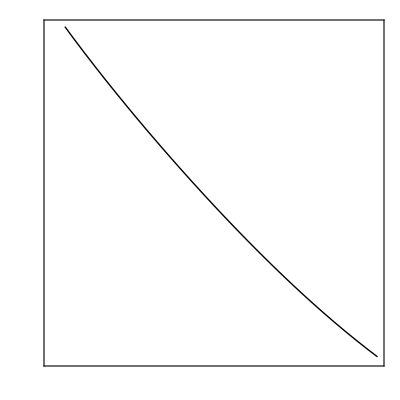

```mathematica
ListPlot[{Transpose[{1000/temps[[1;;31]],Log10[kWag[[1;;31]]]}]},Joined->True,PlotStyle->{{Black}},PlotRange->{{1,4},{-20,-13}},AspectRatio->1,Axes->False,Frame->True,FrameTicks->{Table[{i,"",{If[Mod[i-2,1]==0,0.02,0.01],0}},{i,1,4,0.2}],Table[{i,"",{If[Mod[i+20,2]==0,0.02,0.01],0}},{i,-20,-13,0.5}],{{1000/750,"",{0.02,0}},{1000/500,"",{0.02,0}},{1000/300,"",{0.02,0}},{4,"",{0.02,0}}},Table[{i,"",{If[Mod[i+20,2]==0,0.02,0.01],0}},{i,-20,-13,0.5}]}]
```

```mathematica
kWag[[32;;42]]
```

{3.9567×10^-22,1.1297×10^-20,2.14422×10^-19,2.41237×10^-18,1.71748×10^-17,8.56177×10^-17,3.25321×10^-16,2.63281×10^-15,1.26345×10^-14,4.3062×10^-14,2.62789×10^-13}